# 1 Dimensional FEM - Solver :

Example for a one dimensional diffusion problem with Neumann - Dirichlet boundary conditions

Name : Martin Obermaier
Lehrstuhl Theoretische Elektrotechnik und Prozessmodelle
BTU Cottbus
Datum :

This is a implemenation solves the exquation: kA*u’’-f(x) = 0 ; u(0)= Dir ; u’(L) = Neu

## Setup for the Problem

```mathematica
ClearAll["Global`*"]
Needs["NDSolve`FEM`"];
LaunchKernels[4];
ParallelEvaluate[SystemID];
k=2.0;  (*thermal conductifity*)
L=4.0;      (*length of the object*)
A = 0.1; (*Area*) 
f[x_] := 40*Sin[5*x^0.6]+5;  (*Force*)
Neu[x_] :=  Piecewise[{{10, x==L}},0] ;(*Neuman Boundry*)
Dir[x_]:= Piecewise[{{0, x==0}},None] ; (*Dirrichlet Condition*)
NuNodes = 80;(*Number of Nodes in the problem*)
solution = DSolve[{k*A*y''[x]== -f[x],y[0]==Dir[0],y'[L]==Neu[L]},y[x],x];(*Find the exact solution of the ODE*)
ExactSol[x_] =y[x]/.solution[[1]];
```

## Define the basis functions

```mathematica
Ne[x_,x1_,x2_]:= {{(x-x2)/(x1-x2),(x-x1)/(x2-x1)}}; (*Creation of linear Basisfunctions in 1D*)
Be[x_,x1_,x2_] := D[Ne[a,x1,x2],a]/.a->x;
```

## Calculate mesh

```mathematica
Parallelize[
Coor=Table[i*L/(NuNodes-1),{i,0,NuNodes-1},{j,1}];(*Calculate the Positions of each node*)
Lines =Table[i+j,{i,1,NuNodes-1},{j,0,1}] ;(*Create Elements for ploting*)
mesh= MeshRegion[Coor,Line[Lines]];
NuEl= MeshCellCount[mesh,1]; (*Number of Elements in the mesh*)
NuNoEl=Length[MeshCells[mesh,MeshCellIndex[mesh,1]][[1,1]]];(* Number of Nodes per Elements*)
]
```

## Calculate the elements

```mathematica
Ke[el_]:= k*A*NIntegrate[Transpose[Be[x,Coor[[el,1]],Coor[[el+1,1]]]].Be[x,Coor[[el,1]],Coor[[el+1,1]]],{x,Coor[[el,1]],Coor[[el+1,1]]}]
fe[el_] := NIntegrate[Transpose[Ne[x,Coor[[el,1]],Coor[[el+1,1]]]]*f[x],{x,Coor[[el,1]],Coor[[el+1,1]]},Method->"GaussKronrodRule"] (*Definiton of the forcing element*)
```

## Build the system to be solved

```mathematica
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}]; (*Make SpareArrays additive*)
Parallelize[
pat1=Flatten[Table[Table[i,{i,1,NuNoEl}],NuNoEl]]; (*Create Patterns shift matrices*)
pat2 =Flatten[Table[{i,i},{i,1,NuNoEl}]];

connect=MeshCells[mesh,MeshCellIndex[mesh,1]][[All,1]]; (*Get Conection Matrix*)

Ig=connect [[All, pat1]]; (*First shift matrix*)
Jg=connect [[All, pat2  ]];  (*second shift matrix*)



Kg=ConstantArray[0,{NuEl,NuNoEl^2}]; (*Create a Matrix with one row per Element and one column per entry in the Ke Matrix*)
For[i=1, i≤NuEl, i++,            (*Fill Matrix for each element*)
Kg[[i,All]]=Flatten[Ke[i]] ;  (*Flatten stiffness element*)
]
]
Parallelize[
K1=SparseArray[Transpose[{Flatten[Transpose[Ig]] ,Flatten[Transpose[Jg]]}]->Flatten[Transpose[Kg]]]; (*create stiffness Matrix*)
]


Parallelize[
Fe= ConstantArray[0,{ NuNodes,1}] ; (*Create Forcing-Vector (analog to the Stiffnes Matrix)*)
For[el=1 , el≤ NuEl,el++,
	mi = MeshCells[mesh,MeshCellIndex[mesh,1]][[el,1]];
	For[i = 1,i≤NuNoEl,i++,
                  fi=fe[el];
		ii= mi[[i]];
		Fe[[ii]]=(Fe[[ii]]+fi[[i]]);
	]
	]
]

NeuB= Table[Neu[MeshCoordinates[mesh][[i]][[1]]]*(A*k),{i,1,NuNodes},{j,1}] ;(*Solve for the Neumann vector*)
F1 = Fe+ NeuB;
```

## Solve the system

```mathematica
For[i=1,i≤ NuNodes,i++,
If[Dir[MeshCoordinates[mesh][[i]][[1]]] =!= None,
K=Drop[K1,{i,i},{i,i}];

(*K=Take[K1,{2,NuNodes},{2,NuNodes}];*)
F=Drop[F1,{i}]-Drop[Take[K1,{1,NuNodes},{1,1}],{i}]*Dir[MeshCoordinates[mesh][[i]][[1]]] ;
]
];
d = LinearSolve[K,F]; (*Solve for Nodes and add Dirichlet Node*)
For[i=1,i≤ NuNodes,i++,
If[Dir[MeshCoordinates[mesh][[i]][[1]]] =!= None,
d = Insert[d,{Dir[MeshCoordinates[mesh][[i]][[1]]]},i]
];
]
```

## Plot the solution

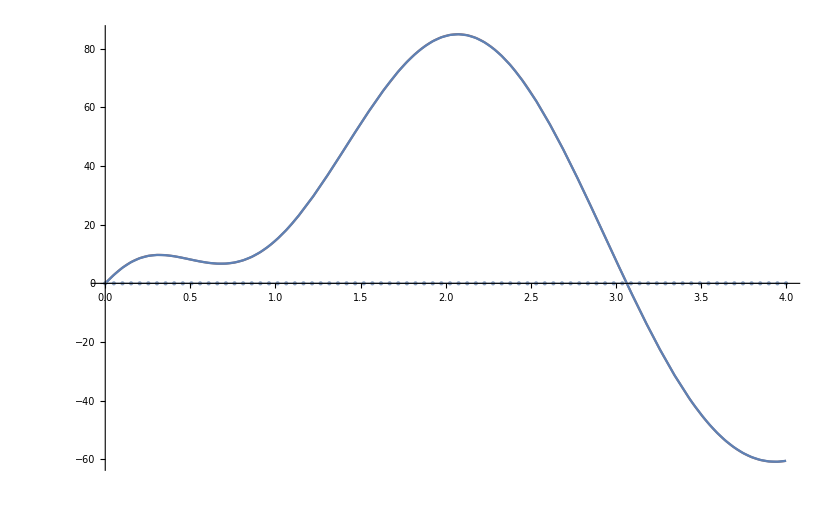

```mathematica
Parallelize[
function =Interpolation[Table[{Coor[[i]][[1]],d[[i]][[1]]},{i,1,NuNodes}],InterpolationOrder->1]; (*Combine the Basisfunctions*)
Show[Plot[ExactSol[x],{x,0,L},ColorFunction->"Rainbow"],Plot[function[x],{x,0,L},PlotRange->All, AxesLabel->{"distance [m]","Temprature [°C]"},AxesOrigin->{0,0}],mesh (*,
HighlightMesh[mesh,Labeled[1,"Index"]]*)]
](*Plot the solutuion*)


CloseKernels[];
```

## Calculate error norms Calculate the L2 Error using the the exact solution:

```mathematica
Parallelize[
ErrL2=Sqrt[NIntegrate[(ExactSol[x]-function[x])^ 2,{x,0,L},Method->"GaussKronrodRule"]]; (*Calculate absulute Error with the L2-Norm*)
RelErrL2 = ErrL2/(Sqrt[NIntegrate[(ExactSol[x])^ 2,{x,0,L},Method->"GaussKronrodRule"]]);   (*Calculate relative Error with the L2-Norm*)
]
Print["The solution has an absultue L2 error of ", ErrL2," and a relative L2 error of ", RelErrL2*100,"%"];
Parallelize[
ErrH1 = Sqrt[NIntegrate[(ExactSol[x]-function[x])^ 2,{x,0,L},Method->"GaussKronrodRule"]+NIntegrate[(D[ExactSol[x]]-D[function[x]])^ 2,{x,0,L},Method->"GaussKronrodRule"]];
RelErrH1 = ErrH1/Sqrt[NIntegrate[(ExactSol[x])^ 2,{x,0,L},Method->"GaussKronrodRule"]+NIntegrate[(D[ExactSol[x]])^ 2,{x,0,L},Method->"GaussKronrodRule"]];
]
Print["The solution has an absultue H1 error of ", ErrH1," and a relative H1 error of ", RelErrH1*100,"%"];
(*ErrPost[i_] := (Coor[[i+1]][[1]]-Coor[[i]][[1]])^ 2 *x/.Last[FindMaximum[Abs[f[x]]/(k*A),{x,Coor[[i]][[1]],Coor[[i+1]][[1]]},MaxIterations->1000]];
Max[Table[ErrPost[i],{i,1,NuEl}]]*)
```

The solution has an absultue L2 error of 0.0683899 and a relative L2 error of 0.0709716%

The solution has an absultue H1 error of 0.0967179 and a relative H1 error of 0.0709716%